# ABC Model

## Model for a particular reaction A + B --> I; I --> 2C

## Default ABC model

a. The maximum timestep exists to ensure that the step size remains below a threshold. It is possible that over time the numeric solution may deviate when the step size is too large. Mathematica automatically sets the step size to minimize deviations and obtain numeric results with extremely high precision. The only practical effect of keeping this value small is to slow down calculations which isn’t very practical at all. If precision is what we are after I would suggest using the PrecisionGoal option rather than MaxStepSize to optimize performance.

The units here are in the same time units that our rate constants use. Since SI units are typically used for these we can assume the units are seconds.

The units of the concentration initialization values are in molarity.

```mathematica
(*Initializing simulation parameters*)
maxTimeStep=10^-6;
maxSteps=Infinity;
timeStart=0;
timeEnd=1;

(*Concentration initialization*)
Ainitial=1; (* default: 1 *)
Binitial=1; (* default: 1 *)
Cinitial=0; (* default: 0 *)
Iinitial=0; (* default: 0 *)

(*Rate constants*)
k1f=1*^1; (* default: 1*^1*)
k1r=1*^1; (* default: 1*^1*)
k2f=1*^1; (* default: 1*^1*)
k2r=0; (*default: 0*) 

(*Get rid of annoying nsolve warnings*)
Off[NSolve::ifun]
```

The differential equations used here are derived from the overall reaction.

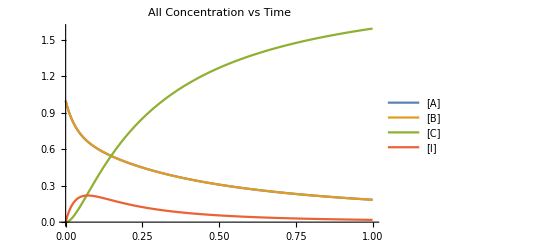

```mathematica
(*Numerical solving of the differential equations*)
data=NDSolve[
{
{Acon'[t]==-k1f*Acon[t]*Bcon[t]+k1r*Icon[t],
Acon[timeStart]==Ainitial},

{Bcon'[t]==-k1f*Acon[t]*Bcon[t]+k1r*Icon[t],
Bcon[timeStart]==Binitial},

{Ccon'[t]==2*k2f*Icon[t]-2*k2r*Ccon[t]^2,
Ccon[timeStart]==Cinitial},

{Icon'[t]==-k2f*Icon[t]+k2r*Ccon[t]^2+k1f*Acon[t]*Bcon[t]-k1r*Icon[t],
Icon[timeStart]==Iinitial}
},
{Acon, Bcon, Ccon, Icon},
{t,timeStart,timeEnd},
MaxStepSize->maxTimeStep,MaxSteps->maxSteps,StartingStepSize-> maxTimeStep];

(*Recoving plots from the solved differential equations*)
Aplot=First[Acon/.data];
Bplot=First[Bcon/.data];
Cplot=First[Ccon/.data];
Iplot=First[Icon/.data];

(*Plotting the concentrations evaluated from the differential equations*)
{(*Plot[Aplot[t],{t,timeStart,timeEnd},PlotLabel->"A Concentration vs Time"],
Plot[Bplot[t],{t,timeStart,timeEnd},PlotLabel->"BCell["",ExpressionUUID->"c10316d1-33f9-4920-8389-3350733f2238"] Concentration vs Time"],
Plot[Cplot[t],{t,timeStart,timeEnd},PlotLabel->"C Concentration vs Time"],
Plot[Iplot[t],{t,timeStart,timeEnd},PlotLabel->"ICell["",ExpressionUUID->"8d715e9c-7807-4c8e-8e50-bc783592dd03"] Concentration vs Time"],*)
Plot[{Aplot[t],Bplot[t], Cplot[t], Iplot[t]},{t,timeStart,timeEnd},PlotLabel->"All Concentration vs Time", PlotLegends->{"[A]","[B]","[C]", "[I]"}]
}//Column
```

## Manipulation of initial concentrations

The next line allows the manipulation of the initial A concentration. If the concentration of A is brought down to 0 we notice that the reaction does not occur and B remains at 1M. If we double the concentration of A we see that the elimination rate of B is higher. As all of B is consumed, the concentration of A drops to 1M and C jumps to 2M instead of rising to an asymptote at around 1.5M. If we begin our reaction with 2M A and 2M B, I reaches its peak concentration much faster and the reaction proceeds quickly until the I peak is reached.

```mathematica
Manipulate[{data=NDSolve[{
{Acon'[t]==-k1f*Acon[t]*Bcon[t]+k1r*Icon[t],
Acon[timeStart]==AinitialManipulate},

{Bcon'[t]==-k1f*Acon[t]*Bcon[t]+k1r*Icon[t],
Bcon[timeStart]==BinitialManipulate},

{Ccon'[t]==2*k2f*Icon[t]-2*k2r*Ccon[t]^2,
Ccon[timeStart]==Cinitial},

{Icon'[t]==-k2f*Icon[t]+k2r*Ccon[t]^2+k1f*Acon[t]*Bcon[t]-k1r*Icon[t],
Icon[timeStart]==Iinitial}
},{Acon, Bcon, Ccon, Icon},{t,timeStart,timeEnd},AccuracyGoal->5];,Aplot=First[Acon/.data];,Bplot=First[Bcon/.data];,Cplot=First[Ccon/.data];,Iplot=First[Icon/.data];,Plot[{Aplot[t],Bplot[t], Cplot[t], Iplot[t]},{t,timeStart,timeEnd},PlotLabel->"All Concentration vs Time", PlotLegends->{"[A]","[B]","[C]", "[I]"}]}[[-1]],{{AinitialManipulate,1}, 0,2},{{BinitialManipulate,1},0,2}]
```

## Sequential case with calculated tmax

The following cell repeats the calculations while forcing all reactions to be sequential. We can also calculate when the intermediate reaches the maximum by solving for the derivative of Iplot[t].

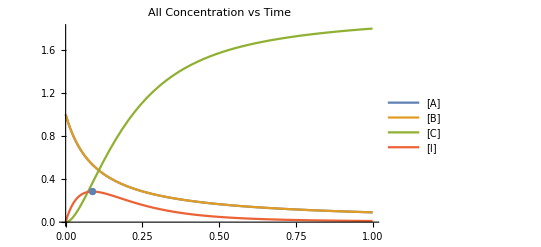

The intermediate reaches its maximum at t→0.0876589

```mathematica
With[{k1r=0, k2r=0},
data=NDSolve[
{
{Acon'[t]==-k1f*Acon[t]*Bcon[t]+k1r*Icon[t],
Acon[timeStart]==Ainitial},

{Bcon'[t]==-k1f*Acon[t]*Bcon[t]+k1r*Icon[t],
Bcon[timeStart]==Binitial},

{Ccon'[t]==2*k2f*Icon[t]-2*k2r*Ccon[t]^2,
Ccon[timeStart]==Cinitial},

{Icon'[t]==-k2f*Icon[t]+k2r*Ccon[t]^2+k1f*Acon[t]*Bcon[t]-k1r*Icon[t],
Icon[timeStart]==Iinitial}
},
{Acon, Bcon, Ccon, Icon},
{t,timeStart,timeEnd}, AccuracyGoal->10]];

Aplot=First[Acon/.data];
Bplot=First[Bcon/.data];
Cplot=First[Ccon/.data];
Iplot=First[Icon/.data];

Iplotmaximum=NSolve[Iplot'[t]==0,t][[1,1]];

Show[{Plot[{Aplot[t],Bplot[t], Cplot[t], Iplot[t]},{t,timeStart,timeEnd},PlotLabel->"All Concentration vs Time", PlotLegends->{"[A]","[B]","[C]", "[I]"}],ListPlot[{{Iplotmaximum[[-1]],Iplot[Iplotmaximum[[-1]]]}}]}]

Print["The intermediate reaches its maximum at ", Iplotmaximum]
```

## Changing the value of K1 by an order of magnitude

The following cell increases the forward rate of the first reaction by a factor of 10 from default. The intermediate time is recalculated and found to happen earlier.

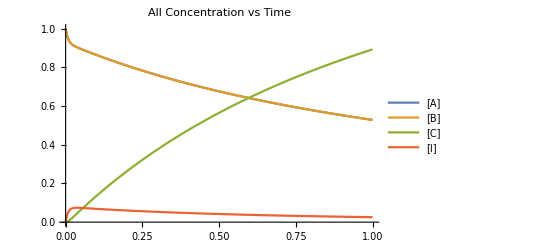

The intermediate reaches its maximum at t→0.0356888

```mathematica
With[{k1r=1*^2},
data=NDSolve[
{
{Acon'[t]==-k1f*Acon[t]*Bcon[t]+k1r*Icon[t],
Acon[timeStart]==Ainitial},

{Bcon'[t]==-k1f*Acon[t]*Bcon[t]+k1r*Icon[t],
Bcon[timeStart]==Binitial},

{Ccon'[t]==2*k2f*Icon[t]-2*k2r*Ccon[t]^2,
Ccon[timeStart]==Cinitial},

{Icon'[t]==-k2f*Icon[t]+k2r*Ccon[t]^2+k1f*Acon[t]*Bcon[t]-k1r*Icon[t],
Icon[timeStart]==Iinitial}
},
{Acon, Bcon, Ccon, Icon},
{t,timeStart,timeEnd}, AccuracyGoal->10]];

Aplot=First[Acon/.data];
Bplot=First[Bcon/.data];
Cplot=First[Ccon/.data];
Iplot=First[Icon/.data];

Plot[{Aplot[t],Bplot[t], Cplot[t], Iplot[t]},{t,timeStart,timeEnd},PlotLabel->"All Concentration vs Time", PlotLegends->{"[A]","[B]","[C]", "[I]"}]

Iplotmaximum=NSolve[Iplot'[t]==0,t][[1,1]];
Print["The intermediate reaches its maximum at ", Iplotmaximum]
```

## tmax: analytic vs. formulaic solution

We can take a plot of tmax against itself for the numerically calculated and for the given equation. We do this by creating a plot of the tmax for a variety of given values of k1f (0 to 1 with steps of 0.001). It appears that the plot is off  by a constant. We still find that the graphs are off though

```mathematica
CalculatedTmax=Interpolation[Table[{k1f,{data=NDSolve[{
{Acon'[t]==-k1f*Acon[t]*Bcon[t],
Acon[timeStart]==Ainitial},

{Bcon'[t]==-k1f*Acon[t]*Bcon[t],
Bcon[timeStart]==Binitial},

{Ccon'[t]==2*k2f*Icon[t],
Ccon[timeStart]==Cinitial},

{Icon'[t]==-k2f*Icon[t]+k1f*Acon[t]*Bcon[t],
Icon[timeStart]==Iinitial}
},{Acon, Bcon, Ccon, Icon},{t,timeStart,timeEnd},AccuracyGoal->10];,Iplot=First[Icon/.data];,Iplotmaximum=NSolve[Iplot'[t]==0,t,WorkingPrecision->30][[1,1,2]]}[[-1]]},{k1f,0,1,.01}]];
```

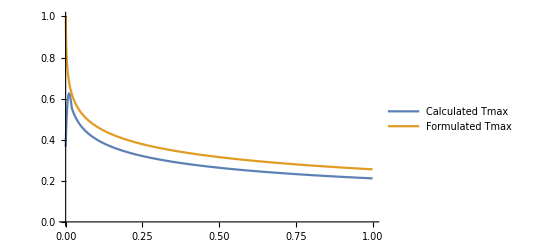

```mathematica
Plot[{CalculatedTmax[k1f],1/(k1f-k2f)Log[k1f/k2f]},{k1f,0,1},PlotRange->{0,1},PlotLegends->{"Calculated Tmax","Formulated Tmax"}]
```

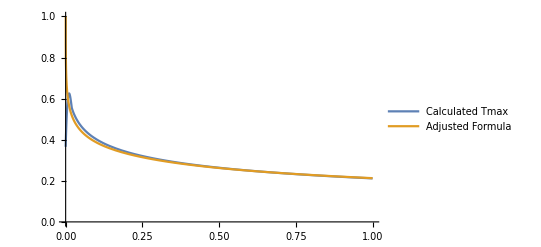

```mathematica
Plot[{CalculatedTmax[k1f],1/(k1f-k2f)Log[k1f/k2f]/Zeta[3]},{k1f,0,1},PlotRange->{0,1},PlotLegends->{"Calculated Tmax","Adjusted Formula"}]
```

It turns out the equation given comes from the textbook where all the stoichiometric ratios are one. If we instead numerically calculate tmax with the reaction A+B--> 2I-->2C and assume [A]=[B] we can then divide the analytic tmax by 2 (since this is a first-order reaction) and achieve the same results.

```mathematica
CalculatedTmax=Interpolation[Table[{k1f,{data=NDSolve[{
{Acon'[t]==-k1f*Acon[t]*Bcon[t],
Acon[timeStart]==Ainitial},

{Bcon'[t]==-k1f*Acon[t]*Bcon[t],
Bcon[timeStart]==Binitial},

{Ccon'[t]==2*k2f*Icon[t],
Ccon[timeStart]==Cinitial},

{Icon'[t]==-2*k2f*Icon[t]+k1f*Acon[t]*Bcon[t],
Icon[timeStart]==Iinitial}
},{Acon, Bcon, Ccon, Icon},{t,timeStart,timeEnd},AccuracyGoal->11];,Iplot=First[Icon/.data];,Iplotmaximum=NSolve[Iplot'[t]==0,t][[1,1,2]]}[[-1]]},{k1f,0,1,.01}]];
```

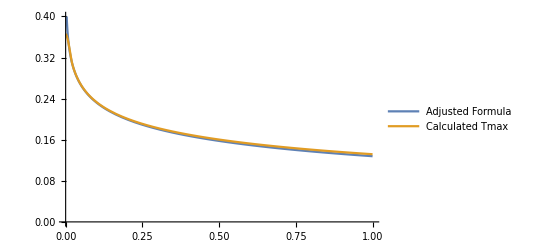

```mathematica
Plot[{1/(k1f-k2f)Log[k1f/k2f]/2,CalculatedTmax[k1f]},{k1f,0,1},PlotRange->{0,.4},PlotLegends->{"Adjusted Formula","Calculated Tmax"}]
```

## Pre-equilibrium (PE) approximation use-case

The following reaction reflects one in which the preequilibrium approximation can be used. The important constraint is k2r==0 && k2f<<k1r. It is clear that there is two sections, one where the intermediate is rapidly formed, then one with the production of product. Tmax and the concentration does change as a result, since the intermediate is dependent on the concentration of all chemicals in solution and all rate constants.

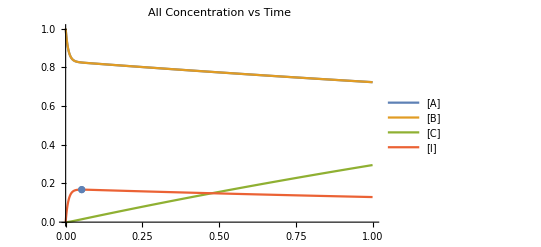

The intermediate reaches its maximum at t→0.0523407

The intermediate reaches its maximum concentration at 0.167923M

```mathematica
With[{k1f=20,k1r=80,k2f=1,k2r=0},
data=NDSolve[{
{Acon'[t]==-k1f*Acon[t]*Bcon[t]+k1r*Icon[t],
Acon[timeStart]==Ainitial},

{Bcon'[t]==-k1f*Acon[t]*Bcon[t]+k1r*Icon[t],
Bcon[timeStart]==Binitial},

{Ccon'[t]==2*k2f*Icon[t]-2*k2r*Ccon[t]^2,
Ccon[timeStart]==Cinitial},

{Icon'[t]==-k2f*Icon[t]+k2r*Ccon[t]^2+k1f*Acon[t]*Bcon[t]-k1r*Icon[t],
Icon[timeStart]==Iinitial}
},
{Acon, Bcon, Ccon, Icon},
{t,timeStart,timeEnd}, AccuracyGoal->10]
];

Aplot=First[Acon/.data];
Bplot=First[Bcon/.data];
Cplot=First[Ccon/.data];
Iplot=First[Icon/.data];

Iplotmaximum=NSolve[Iplot'[t]==0,t][[1,1]];
IplotmaximumC=Iplot[Iplotmaximum[[2]]];

Show[{Plot[{Aplot[t],Bplot[t], Cplot[t], Iplot[t]},{t,timeStart,timeEnd},PlotLabel->"All Concentration vs Time", PlotLegends->{"[A]","[B]","[C]", "[I]"}],ListPlot[{{Iplotmaximum[[2]],IplotmaximumC}}]}]

Print["The intermediate reaches its maximum at ", Iplotmaximum]
Print["The intermediate reaches its maximum concentration at ", IplotmaximumC,"M"]
```

## Steady-state approximation

The steady state approximation assumes that no intermediate is formed because the formation of products is much faster than the formation of intermediate. The following situation may reflect one where the steady state approximation can be used.

One can easily see that [I] remains nearly constant the entire time. The peak concentration reached is less than 0.5% of [A]0 + [B]0

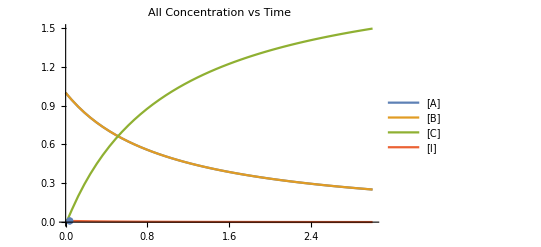

The intermediate reaches its maximum at t→0.039991

The intermediate reaches its maximum concentration at 0.00915953M

```mathematica
With[{k1f=1,k1r=1,k2f=100,k2r=0,timeEnd=3},
data=NDSolve[{
{Acon'[t]==-k1f*Acon[t]*Bcon[t]+k1r*Icon[t],
Acon[timeStart]==Ainitial},

{Bcon'[t]==-k1f*Acon[t]*Bcon[t]+k1r*Icon[t],
Bcon[timeStart]==Binitial},

{Ccon'[t]==2*k2f*Icon[t]-2*k2r*Ccon[t]^2,
Ccon[timeStart]==Cinitial},

{Icon'[t]==-k2f*Icon[t]+k2r*Ccon[t]^2+k1f*Acon[t]*Bcon[t]-k1r*Icon[t],
Icon[timeStart]==Iinitial}
},
{Acon, Bcon, Ccon, Icon},
{t,timeStart,timeEnd}, AccuracyGoal->10]
];

Aplot=First[Acon/.data];
Bplot=First[Bcon/.data];
Cplot=First[Ccon/.data];
Iplot=First[Icon/.data];

Iplotmaximum=NSolve[Iplot'[t]==0,t][[1,1]];
IplotmaximumC=Iplot[Iplotmaximum[[2]]];

Show[{Plot[{Aplot[t],Bplot[t], Cplot[t], Iplot[t]},{t,timeStart,3},PlotLabel->"All Concentration vs Time", PlotLegends->{"[A]","[B]","[C]", "[I]"}],ListPlot[{{Iplotmaximum[[2]],IplotmaximumC}}]}]

Print["The intermediate reaches its maximum at ", Iplotmaximum]
Print["The intermediate reaches its maximum concentration at ", IplotmaximumC,"M"]
```